```mathematica
IntegralFactor = Integrate[d^7/(7/5*d^12+1), {d, 0, Infinity}]
```

((5/7)^(2/3) π)/(6 √3)

100000000

7^(1/12)/(10 2^(1/3) 5^(5/12))

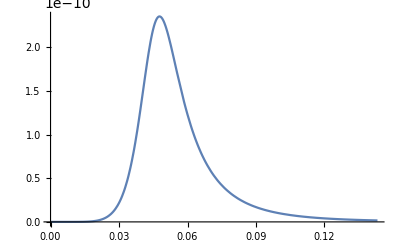

0.0477358

```mathematica
H=100000000
r0=(7/5)^(1/12)/H^(1/6)
Plot[r^7/(H^2*r^12 +1), {r, 0, 3r0}, PlotRange->Full]
N[(7/5)^(1/12)*H^(-1/6)]
```

```mathematica
(* Check final result *)

H=10^12;
r0=(7/5)^(1/12)/H^(1/6);
NIntegrate[r^7/(H^2*r^12+1), {r, 0, Infinity}]
N[Pi/6/Sqrt[3]*H^(-4/3)]
```

3.023×10^-17

3.023×10^-17

```mathematica
0.71
```

```mathematica
Clear[H]
Solve[D[r^7/(H^2*r^12 +1),r]==0, r]
```

{{r→0},{r→0},{r→0},{r→0},{r→0},{r→0},{r→-(7/5)^(1/12)/H^(1/6)},{r→-(ⅈ (7/5)^(1/12))/H^(1/6)},{r→(ⅈ (7/5)^(1/12))/H^(1/6)},{r→(7/5)^(1/12)/H^(1/6)},{r→-((-1)^(1/6) (7/5)^(1/12))/H^(1/6)},{r→-((-1)^(1/3) (7/5)^(1/12))/H^(1/6)},{r→((-1)^(1/3) (7/5)^(1/12))/H^(1/6)},{r→-((-1)^(2/3) (7/5)^(1/12))/H^(1/6)},{r→((-1)^(2/3) (7/5)^(1/12))/H^(1/6)},{r→-((-1)^(5/6) (7/5)^(1/12))/H^(1/6)},{r→((-1)^(5/6) (7/5)^(1/12))/H^(1/6)},{r→((-1)^(1/6) 7^(1/12))/(5^(1/12) H^(1/6))}}

```mathematica
Clear[H]
r^7/(H^2*r^12 +1)/.{r->-(7/5)^(1/12)/H^(1/6)}
```

-(5^(5/12) 7^(7/12))/(12 H^(7/6))

```mathematica
Integrate[r^7/(H^2 * r^12 + 1), {r, 0, Infinity}]
```

$Aborted

```mathematica
Series[r^7/( r^12 + ϵ),{ϵ,0,2}]
```

1/r^5-ϵ/r^17+ϵ^2/r^29+O[ϵ]^3

```mathematica
ϵ=10^-9;
NIntegrate[r^7/(r^12+ϵ)*ϵ, {r,0,Infinity}]
```

3.023×10^-7

```mathematica
(* Taylor expand around Subscript[ρ, 0]*)
Clear[ϵ]
Series[r^7/(r^12+ϵ), {r, r0, 2}]
```

r0^7/(r0^12+ϵ)+((-5 r0^18+7 r0^6 ϵ) (r-r0))/((r0^12+ϵ)^2)+(3 (5 r0^29-36 r0^17 ϵ+7 r0^5 ϵ^2) (r-r0)^2)/((r0^12+ϵ)^3)+O[r-r0]^3

```mathematica
(10^10)^(2/3)*4*Pi/6/Sqrt[3]/Sqrt[2^12*Factorial[3]^4]*NIntegrate[R^13*Exp[-R^2], {R, 0, Infinity}]
```

876970.

```mathematica
-N[(10^10)^(2/3)*Pi/3/Sqrt[3]/Sqrt[2^12*Factorial[3]^4]*Factorial[6]]
```

-876970.

```mathematica
Integrate[R^(2A+1)*Exp[-R^2], {R, 0, Infinity}, Assumptions->{A∈Integers, A>0}]
```

1/2 Gamma[1+A]

```mathematica
1/2 Gamma[1+A]/.{A->10}
```

1814400

```mathematica
Factorial[10]
```

3628800

```mathematica
(* Check rho integral*)
(* this should be 1 *)
NIntegrate[r^7/(10^20*r^12+1), {r, 0, Infinity}]*Sqrt[3]*6/Pi*(10^10)^(4/3)
```

```mathematica
H=10^4;

(* The analytical result *)
analytical = -N[(H)^(2/3)*Pi/3/Sqrt[3]/Sqrt[2^12*Factorial[3]^4]*Factorial[6]]

(* The original integral *)

L = 3;
integrand = r1*r2*((r1*Sin[theta])^2+(r1*Cos[theta]-r2)^2)^(-3)/Abs[H*I+((r1*Sin[theta])^2+(r1*Cos[theta]-r2)^2)^(-3)]^2*(1/Sqrt[2*Pi*2^L*Factorial[L]]*r1^L*Exp[-r1^2/4])*(1/Sqrt[2*Pi*2^L*Factorial[L]]*r1^L*Exp[-r1^2/4])*(1/Sqrt[2*Pi*2^L*Factorial[L]]*r2^L*Exp[-r2^2/4])*(1/Sqrt[2*Pi*2^L*Factorial[L]]*r2^L*Exp[-r2^2/4])*4;
integral = -2*Pi *H^(2/3)*NIntegrate[H^(4/3)*integrand, {r1, 0, Infinity}, {r2, 0, Infinity}, {theta, 0, 2*Pi},WorkingPrecision->MachinePrecision]
integral/analytical
```

-87.697

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0294795+0. ⅈ and 7.61641×10^-6 for the integral and error estimates.

-85.974

0.980353

```mathematica
ScientificForm[0.5106791975841121]
```

5.10679×10^-1

```mathematica
N[MachinePrecision]
```

15.9546

```mathematica
N[Log[1.1,10]]
```

24.1589

```mathematica
LLLr[l_,r_]:=r^l*Exp[-r^2/4]/Sqrt[2*Pi*2^l]/Factorial[l]
```

```mathematica
(* Mathematica knows tricks for these small H integrals! *)
a=5; b=5; c=5; d=5;
Cintegrand = 2*Pi*r1*r2*(r1^2 + r2^2 - 2*r1*r2*Cos[θ])^3*(LLLr[a,r1]*LLLr[b,r2]*Exp[-I*a*θ]+LLLr[a,r2]*LLLr[b,r1]*Exp[-I*b*θ])*(LLLr[c,r1]*LLLr[d,r2]*Exp[I*c*θ]+LLLr[c,r2]*LLLr[d,r1]*Exp[I*d*θ]);
Cresult =Integrate[Cintegrand, {r1, 0, Infinity}, {r2, 0, Infinity}, {θ,-Pi, Pi}, Assumptions->{θ∈Reals,a+b==c+d,r1>=0, r2>=0,a∈Integers,a>=0,b∈Integers,c∈Integers,d∈Integers}]
```

868/75

```mathematica
(* Mathematica knows tricks for these small H integrals! *)
Clear[a,b,c,d]
LLLr[l_,r_]:=r^l*Exp[-r^2/4]/Sqrt[2*Pi*2^l]/Factorial[l]
Cintegrand = 2*Pi*r1*r2*(r1^2 + r2^2 - 2*r1*r2*Cos[θ])^3*(LLLr[a,r1]*LLLr[b,r2]+LLLr[a,r2]*LLLr[b,r1])*(LLLr[c,r1]*LLLr[d,r2]+LLLr[c,r2]*LLLr[d,r1]);
Cresult =Integrate[Cintegrand, {r1, 0, Infinity}, {r2, 0, Infinity}, {θ,-Pi, Pi}, Assumptions->{θ∈Reals,a+b==c+d,r1>=0, r2>=0,a∈Integers,a>=0,b∈Integers,c∈Integers,d∈Integers}]
```

1/(a! b! c! d!)2^(-c-d) (Gamma[1+b/2+c/2] Gamma[1+a/2+d/2] (2^((a+d)/2) (2+b+c) (4+b+c) (6+b+c) (Cosh[1/2 b Log[2]]+Sinh[1/2 b Log[2]]) (Cosh[1/2 c Log[2]]+Sinh[1/2 c Log[2]])+9 2^(a/2+d/2) (2+b+c) (4+b+c) (2+a+d) (Cosh[1/2 b Log[2]]+Sinh[1/2 b Log[2]]) (Cosh[1/2 c Log[2]]+Sinh[1/2 c Log[2]])+9 2^(a/2+d/2) (2+b+c) (2+a+d) (4+a+d) (Cosh[1/2 b Log[2]]+Sinh[1/2 b Log[2]]) (Cosh[1/2 c Log[2]]+Sinh[1/2 c Log[2]])+2^(a/2+d/2) (2+a+d) (4+a+d) (6+a+d) (Cosh[1/2 b Log[2]]+Sinh[1/2 b Log[2]]) (Cosh[1/2 c Log[2]]+Sinh[1/2 c Log[2]])+2^(b/2+c/2) (2+b+c) (4+b+c) (6+b+c) (Cosh[1/2 a Log[2]]+Sinh[1/2 a Log[2]]) (Cosh[1/2 d Log[2]]+Sinh[1/2 d Log[2]])+9 2^(b/2+c/2) (2+b+c) (4+b+c) (2+a+d) (Cosh[1/2 a Log[2]]+Sinh[1/2 a Log[2]]) (Cosh[1/2 d Log[2]]+Sinh[1/2 d Log[2]])+9 2^(b/2+c/2) (2+b+c) (2+a+d) (4+a+d) (Cosh[1/2 a Log[2]]+Sinh[1/2 a Log[2]]) (Cosh[1/2 d Log[2]]+Sinh[1/2 d Log[2]])+2^((b+c)/2) (2+a+d) (4+a+d) (6+a+d) (Cosh[1/2 a Log[2]]+Sinh[1/2 a Log[2]]) (Cosh[1/2 d Log[2]]+Sinh[1/2 d Log[2]]))+Gamma[1+a/2+c/2] Gamma[1+b/2+d/2] (2^((b+d)/2) (2+a+c) (4+a+c) (6+a+c) (Cosh[1/2 a Log[2]]+Sinh[1/2 a Log[2]]) (Cosh[1/2 c Log[2]]+Sinh[1/2 c Log[2]])+9 2^(b/2+d/2) (2+a+c) (4+a+c) (2+b+d) (Cosh[1/2 a Log[2]]+Sinh[1/2 a Log[2]]) (Cosh[1/2 c Log[2]]+Sinh[1/2 c Log[2]])+9 2^(b/2+d/2) (2+a+c) (2+b+d) (4+b+d) (Cosh[1/2 a Log[2]]+Sinh[1/2 a Log[2]]) (Cosh[1/2 c Log[2]]+Sinh[1/2 c Log[2]])+2^(b/2+d/2) (2+b+d) (4+b+d) (6+b+d) (Cosh[1/2 a Log[2]]+Sinh[1/2 a Log[2]]) (Cosh[1/2 c Log[2]]+Sinh[1/2 c Log[2]])+2^(a/2+c/2) (2+a+c) (4+a+c) (6+a+c) (Cosh[1/2 b Log[2]]+Sinh[1/2 b Log[2]]) (Cosh[1/2 d Log[2]]+Sinh[1/2 d Log[2]])+9 2^(a/2+c/2) (2+a+c) (4+a+c) (2+b+d) (Cosh[1/2 b Log[2]]+Sinh[1/2 b Log[2]]) (Cosh[1/2 d Log[2]]+Sinh[1/2 d Log[2]])+9 2^(a/2+c/2) (2+a+c) (2+b+d) (4+b+d) (Cosh[1/2 b Log[2]]+Sinh[1/2 b Log[2]]) (Cosh[1/2 d Log[2]]+Sinh[1/2 d Log[2]])+2^((a+c)/2) (2+b+d) (4+b+d) (6+b+d) (Cosh[1/2 b Log[2]]+Sinh[1/2 b Log[2]]) (Cosh[1/2 d Log[2]]+Sinh[1/2 d Log[2]])))

```mathematica
(* Here's the full solution from Mathematica for C IF I drop the phase terms (valid if a=b=c=d, at least) *)
Callequal=1/(a! b! c! d!)2^(-c-d) (Gamma[1+b/2+c/2] Gamma[1+a/2+d/2] (2^((a+d)/2) (2+b+c) (4+b+c) (6+b+c) (Cosh[1/2 b Log[2]]+Sinh[1/2 b Log[2]]) (Cosh[1/2 c Log[2]]+Sinh[1/2 c Log[2]])+9 2^(a/2+d/2) (2+b+c) (4+b+c) (2+a+d) (Cosh[1/2 b Log[2]]+Sinh[1/2 b Log[2]]) (Cosh[1/2 c Log[2]]+Sinh[1/2 c Log[2]])+9 2^(a/2+d/2) (2+b+c) (2+a+d) (4+a+d) (Cosh[1/2 b Log[2]]+Sinh[1/2 b Log[2]]) (Cosh[1/2 c Log[2]]+Sinh[1/2 c Log[2]])+2^(a/2+d/2) (2+a+d) (4+a+d) (6+a+d) (Cosh[1/2 b Log[2]]+Sinh[1/2 b Log[2]]) (Cosh[1/2 c Log[2]]+Sinh[1/2 c Log[2]])+2^(b/2+c/2) (2+b+c) (4+b+c) (6+b+c) (Cosh[1/2 a Log[2]]+Sinh[1/2 a Log[2]]) (Cosh[1/2 d Log[2]]+Sinh[1/2 d Log[2]])+9 2^(b/2+c/2) (2+b+c) (4+b+c) (2+a+d) (Cosh[1/2 a Log[2]]+Sinh[1/2 a Log[2]]) (Cosh[1/2 d Log[2]]+Sinh[1/2 d Log[2]])+9 2^(b/2+c/2) (2+b+c) (2+a+d) (4+a+d) (Cosh[1/2 a Log[2]]+Sinh[1/2 a Log[2]]) (Cosh[1/2 d Log[2]]+Sinh[1/2 d Log[2]])+2^((b+c)/2) (2+a+d) (4+a+d) (6+a+d) (Cosh[1/2 a Log[2]]+Sinh[1/2 a Log[2]]) (Cosh[1/2 d Log[2]]+Sinh[1/2 d Log[2]]))+Gamma[1+a/2+c/2] Gamma[1+b/2+d/2] (2^((b+d)/2) (2+a+c) (4+a+c) (6+a+c) (Cosh[1/2 a Log[2]]+Sinh[1/2 a Log[2]]) (Cosh[1/2 c Log[2]]+Sinh[1/2 c Log[2]])+9 2^(b/2+d/2) (2+a+c) (4+a+c) (2+b+d) (Cosh[1/2 a Log[2]]+Sinh[1/2 a Log[2]]) (Cosh[1/2 c Log[2]]+Sinh[1/2 c Log[2]])+9 2^(b/2+d/2) (2+a+c) (2+b+d) (4+b+d) (Cosh[1/2 a Log[2]]+Sinh[1/2 a Log[2]]) (Cosh[1/2 c Log[2]]+Sinh[1/2 c Log[2]])+2^(b/2+d/2) (2+b+d) (4+b+d) (6+b+d) (Cosh[1/2 a Log[2]]+Sinh[1/2 a Log[2]]) (Cosh[1/2 c Log[2]]+Sinh[1/2 c Log[2]])+2^(a/2+c/2) (2+a+c) (4+a+c) (6+a+c) (Cosh[1/2 b Log[2]]+Sinh[1/2 b Log[2]]) (Cosh[1/2 d Log[2]]+Sinh[1/2 d Log[2]])+9 2^(a/2+c/2) (2+a+c) (4+a+c) (2+b+d) (Cosh[1/2 b Log[2]]+Sinh[1/2 b Log[2]]) (Cosh[1/2 d Log[2]]+Sinh[1/2 d Log[2]])+9 2^(a/2+c/2) (2+a+c) (2+b+d) (4+b+d) (Cosh[1/2 b Log[2]]+Sinh[1/2 b Log[2]]) (Cosh[1/2 d Log[2]]+Sinh[1/2 d Log[2]])+2^((a+c)/2) (2+b+d) (4+b+d) (6+b+d) (Cosh[1/2 b Log[2]]+Sinh[1/2 b Log[2]]) (Cosh[1/2 d Log[2]]+Sinh[1/2 d Log[2]])));
FullSimplify[Callequal/.{b->a, c->a, d->a},Assumptions->{θ∈Reals,a+b==c+d,r1>=0, r2>=0,a∈Integers,a>=0,b∈Integers,c∈Integers,d∈Integers}]
```

(128 (1+a) (2+a) (6+5 a))/(a!)^2

```mathematica
FullSimplify[Callequal,Assumptions->{θ∈Reals,a+b==c+d,r1>=0, r2>=0,a∈Integers,a>=0,b∈Integers,c∈Integers,d∈Integers}]
```

$Aborted

```mathematica
Cresult*Sqrt[a! * b! * c! * d!]/1536
Cresult*Sqrt[a! * b! * c! * d!]*2^(a+b+c+d)/2/1536
```

217/2

56885248

```mathematica
(* Mathematica knows tricks for these small H integrals! *)
Clear[a,b,c,d]
Cintegrand = 2*Pi*r1*r2*(r1^2 + r2^2 - 2*r1*r2*Cos[θ])^3*(LLLr[a,r1]*LLLr[b,r2]*Exp[-I*a*θ]+LLLr[a,r2]*LLLr[b,r1]*Exp[-I*b*θ])*(LLLr[c,r1]*LLLr[d,r2]*Exp[I*c*θ]+LLLr[c,r2]*LLLr[d,r1]*Exp[I*d*θ]);
Cresult =Integrate[Cintegrand, {r1, 0, Infinity}, {r2, 0, Infinity}, {θ,-Pi, Pi}, Assumptions->{θ∈Reals,a+b==c+d,r1>=0, r2>=0,a∈Integers,a>=0,b∈Integers,c∈Integers,d∈Integers}]
```

$Aborted

```mathematica
520/3/1536
```

65/576

```mathematica
6144/1536
```

4

```mathematica
(4/(11/2))
```

8/11

```mathematica
Clear[a,b,c,d]
Cintegrand = 2*Pi*r1*r2*(r1^2 + r2^2 - 2*r1*r2*Cos[θ])^3*(LLLr[a,r1]*LLLr[b,r2]*Exp[-I*a*θ]+LLLr[a,r2]*LLLr[b,r1]*Exp[-I*b*θ])*(LLLr[c,r1]*LLLr[d,r2]*Exp[I*c*θ]+LLLr[c,r2]*LLLr[d,r1]*Exp[I*d*θ]);
FullSimplify[Cintegrand,Assumptions->{θ∈Reals,a+b==c+d,r1>=0, r2>=0,a∈Integers,a>=0,b∈Integers,c∈Integers,d∈Integers}]
```

$Aborted

```mathematica
1/(π a! b! c! d!)2^(-1-c-d) ⅇ^(-r1^2/2-r2^2/2-ⅈ (c+d) θ) r1 r2 (ⅇ^(ⅈ a θ) r1^b r2^a+ⅇ^(ⅈ b θ) r1^a r2^b) (ⅇ^(ⅈ d θ) r1^d r2^c+ⅇ^(ⅈ c θ) r1^c r2^d) (r1^2+r2^2-2 r1 r2 Cos[θ])^3
```

```mathematica
(* Latest attempt ; multiply everything out first, so that you can separate all the integrals *)
(* USE A SIMPLER LLLr which doesn't include the numerical factors, which you can put in by hand at the end *)
LLLrS[l_,r_]:=r^l*Exp[-r^2/4]
Cintegrand = 2*Pi*r1*r2*(r1^2 + r2^2 - 2*r1*r2*Cos[θ])^3*(LLLrS[a,r1]*LLLrS[b,r2]*Exp[-I*a*θ]+LLLrS[a,r2]*LLLrS[b,r1]*Exp[-I*b*θ])*(LLLrS[c,r1]*LLLrS[d,r2]*Exp[I*c*θ]+LLLrS[c,r2]*LLLrS[d,r1]*Exp[I*d*θ]);
Cintegrandexpanded = ExpandAll[Cintegrand]
(*Integrate[Cintegrandexpanded, {θ,-Pi,Pi},Assumptions->{θ∈Reals,a+b==c+d,r1>=0, r2>=0,a∈Integers,a>=0,b∈Integers,c∈Integers,d∈Integers}]*)
```

2 ⅇ^(-r1^2/2-r2^2/2-ⅈ b θ+ⅈ d θ) π r1^(7+b+d) r2^(1+a+c)+6 ⅇ^(-r1^2/2-r2^2/2-ⅈ b θ+ⅈ d θ) π r1^(5+b+d) r2^(3+a+c)+6 ⅇ^(-r1^2/2-r2^2/2-ⅈ b θ+ⅈ d θ) π r1^(3+b+d) r2^(5+a+c)+2 ⅇ^(-r1^2/2-r2^2/2-ⅈ b θ+ⅈ d θ) π r1^(1+b+d) r2^(7+a+c)+2 ⅇ^(-r1^2/2-r2^2/2-ⅈ a θ+ⅈ d θ) π r1^(7+a+d) r2^(1+b+c)+6 ⅇ^(-r1^2/2-r2^2/2-ⅈ a θ+ⅈ d θ) π r1^(5+a+d) r2^(3+b+c)+6 ⅇ^(-r1^2/2-r2^2/2-ⅈ a θ+ⅈ d θ) π r1^(3+a+d) r2^(5+b+c)+2 ⅇ^(-r1^2/2-r2^2/2-ⅈ a θ+ⅈ d θ) π r1^(1+a+d) r2^(7+b+c)+2 ⅇ^(-r1^2/2-r2^2/2-ⅈ b θ+ⅈ c θ) π r1^(7+b+c) r2^(1+a+d)+6 ⅇ^(-r1^2/2-r2^2/2-ⅈ b θ+ⅈ c θ) π r1^(5+b+c) r2^(3+a+d)+6 ⅇ^(-r1^2/2-r2^2/2-ⅈ b θ+ⅈ c θ) π r1^(3+b+c) r2^(5+a+d)+2 ⅇ^(-r1^2/2-r2^2/2-ⅈ b θ+ⅈ c θ) π r1^(1+b+c) r2^(7+a+d)+2 ⅇ^(-r1^2/2-r2^2/2-ⅈ a θ+ⅈ c θ) π r1^(7+a+c) r2^(1+b+d)+6 ⅇ^(-r1^2/2-r2^2/2-ⅈ a θ+ⅈ c θ) π r1^(5+a+c) r2^(3+b+d)+6 ⅇ^(-r1^2/2-r2^2/2-ⅈ a θ+ⅈ c θ) π r1^(3+a+c) r2^(5+b+d)+2 ⅇ^(-r1^2/2-r2^2/2-ⅈ a θ+ⅈ c θ) π r1^(1+a+c) r2^(7+b+d)-12 ⅇ^(-r1^2/2-r2^2/2-ⅈ b θ+ⅈ d θ) π r1^(6+b+d) r2^(2+a+c) Cos[θ]-24 ⅇ^(-r1^2/2-r2^2/2-ⅈ b θ+ⅈ d θ) π r1^(4+b+d) r2^(4+a+c) Cos[θ]-12 ⅇ^(-r1^2/2-r2^2/2-ⅈ b θ+ⅈ d θ) π r1^(2+b+d) r2^(6+a+c) Cos[θ]-12 ⅇ^(-r1^2/2-r2^2/2-ⅈ a θ+ⅈ d θ) π r1^(6+a+d) r2^(2+b+c) Cos[θ]-24 ⅇ^(-r1^2/2-r2^2/2-ⅈ a θ+ⅈ d θ) π r1^(4+a+d) r2^(4+b+c) Cos[θ]-12 ⅇ^(-r1^2/2-r2^2/2-ⅈ a θ+ⅈ d θ) π r1^(2+a+d) r2^(6+b+c) Cos[θ]-12 ⅇ^(-r1^2/2-r2^2/2-ⅈ b θ+ⅈ c θ) π r1^(6+b+c) r2^(2+a+d) Cos[θ]-24 ⅇ^(-r1^2/2-r2^2/2-ⅈ b θ+ⅈ c θ) π r1^(4+b+c) r2^(4+a+d) Cos[θ]-12 ⅇ^(-r1^2/2-r2^2/2-ⅈ b θ+ⅈ c θ) π r1^(2+b+c) r2^(6+a+d) Cos[θ]-12 ⅇ^(-r1^2/2-r2^2/2-ⅈ a θ+ⅈ c θ) π r1^(6+a+c) r2^(2+b+d) Cos[θ]-24 ⅇ^(-r1^2/2-r2^2/2-ⅈ a θ+ⅈ c θ) π r1^(4+a+c) r2^(4+b+d) Cos[θ]-12 ⅇ^(-r1^2/2-r2^2/2-ⅈ a θ+ⅈ c θ) π r1^(2+a+c) r2^(6+b+d) Cos[θ]+24 ⅇ^(-r1^2/2-r2^2/2-ⅈ b θ+ⅈ d θ) π r1^(5+b+d) r2^(3+a+c) Cos[θ]^2+24 ⅇ^(-r1^2/2-r2^2/2-ⅈ b θ+ⅈ d θ) π r1^(3+b+d) r2^(5+a+c) Cos[θ]^2+24 ⅇ^(-r1^2/2-r2^2/2-ⅈ a θ+ⅈ d θ) π r1^(5+a+d) r2^(3+b+c) Cos[θ]^2+24 ⅇ^(-r1^2/2-r2^2/2-ⅈ a θ+ⅈ d θ) π r1^(3+a+d) r2^(5+b+c) Cos[θ]^2+24 ⅇ^(-r1^2/2-r2^2/2-ⅈ b θ+ⅈ c θ) π r1^(5+b+c) r2^(3+a+d) Cos[θ]^2+24 ⅇ^(-r1^2/2-r2^2/2-ⅈ b θ+ⅈ c θ) π r1^(3+b+c) r2^(5+a+d) Cos[θ]^2+24 ⅇ^(-r1^2/2-r2^2/2-ⅈ a θ+ⅈ c θ) π r1^(5+a+c) r2^(3+b+d) Cos[θ]^2+24 ⅇ^(-r1^2/2-r2^2/2-ⅈ a θ+ⅈ c θ) π r1^(3+a+c) r2^(5+b+d) Cos[θ]^2-16 ⅇ^(-r1^2/2-r2^2/2-ⅈ b θ+ⅈ d θ) π r1^(4+b+d) r2^(4+a+c) Cos[θ]^3-16 ⅇ^(-r1^2/2-r2^2/2-ⅈ a θ+ⅈ d θ) π r1^(4+a+d) r2^(4+b+c) Cos[θ]^3-16 ⅇ^(-r1^2/2-r2^2/2-ⅈ b θ+ⅈ c θ) π r1^(4+b+c) r2^(4+a+d) Cos[θ]^3-16 ⅇ^(-r1^2/2-r2^2/2-ⅈ a θ+ⅈ c θ) π r1^(4+a+c) r2^(4+b+d) Cos[θ]^3

```mathematica
Integrate[ⅇ^(-ⅈ b θ+ⅈ d θ) Cos[θ]^3,{θ,-Pi,Pi},Assumptions->{b∈Integers,d∈Integers}]
```

-(2 (-7+(b-d)^2) (b-d) Sin[(b-d) π])/((-3+b-d) (-1+b-d) (1+b-d) (3+b-d))

```mathematica
(* Dealing with the θ INTEGRATION by hand lolz *)
2π(2 ⅇ^(-r1^2/2-r2^2/2) π r1^(7+b+d) r2^(1+a+c)d,b+6 ⅇ^(-r1^2/2-r2^2/2) π r1^(5+b+d) r2^(3+a+c)d,b+6 ⅇ^(-r1^2/2-r2^2/2) π r1^(3+b+d) r2^(5+a+c)d,b+2 ⅇ^(-r1^2/2-r2^2/2) π r1^(1+b+d) r2^(7+a+c)d,b+2 ⅇ^(-r1^2/2-r2^2/2) π r1^(7+a+d) r2^(1+b+c)d,a+6 ⅇ^(-r1^2/2-r2^2/2) π r1^(5+a+d) r2^(3+b+c)d,a+6 ⅇ^(-r1^2/2-r2^2/2) π r1^(3+a+d) r2^(5+b+c)d,a+2 ⅇ^(-r1^2/2-r2^2/2) π r1^(1+a+d) r2^(7+b+c)d,a+2 ⅇ^(-r1^2/2-r2^2/2) π r1^(7+b+c) r2^(1+a+d)b,c+6 ⅇ^(-r1^2/2-r2^2/2) π r1^(5+b+c) r2^(3+a+d)b,c+6 ⅇ^(-r1^2/2-r2^2/2) π r1^(3+b+c) r2^(5+a+d)b,c+2 ⅇ^(-r1^2/2-r2^2/2) π r1^(1+b+c) r2^(7+a+d)b,c+2 ⅇ^(-r1^2/2-r2^2/2) π r1^(7+a+c) r2^(1+b+d)a,c+6 ⅇ^(-r1^2/2-r2^2/2) π r1^(5+a+c) r2^(3+b+d)a,c+6 ⅇ^(-r1^2/2-r2^2/2) π r1^(3+a+c) r2^(5+b+d)a,c+2 ⅇ^(-r1^2/2-r2^2/2) π r1^(1+a+c) r2^(7+b+d)a,c-12 ⅇ^(-r1^2/2-r2^2/2) π r1^(6+b+d) r2^(2+a+c) (d-b,1 +d-b,-1 )/2-24 ⅇ^(-r1^2/2-r2^2/2) π r1^(4+b+d) r2^(4+a+c) (d-b,1 +d-b,-1 )/2-12 ⅇ^(-r1^2/2-r2^2/2) π r1^(2+b+d) r2^(6+a+c) (d-b,1 +d-b,-1 )/2-12 ⅇ^(-r1^2/2-r2^2/2) π r1^(6+a+d) r2^(2+b+c) (d-a,1 +d-a,-1 )/2-24 ⅇ^(-r1^2/2-r2^2/2) π r1^(4+a+d) r2^(4+b+c) (d-a,1 +d-a,-1 )/2-12 ⅇ^(-r1^2/2-r2^2/2) π r1^(2+a+d) r2^(6+b+c) (d-a,1 +d-a,-1 )/2-12 ⅇ^(-r1^2/2-r2^2/2) π r1^(6+b+c) r2^(2+a+d) (b-c,1 +b-c,-1 )/2-24 ⅇ^(-r1^2/2-r2^2/2) π r1^(4+b+c) r2^(4+a+d) (b-c,1 +b-c,-1 )/2-12 ⅇ^(-r1^2/2-r2^2/2) π r1^(2+b+c) r2^(6+a+d) (b-c,1 +b-c,-1 )/2-12 ⅇ^(-r1^2/2-r2^2/2) π r1^(6+a+c) r2^(2+b+d) (a-c,1 +a-c,-1 )/2-24 ⅇ^(-r1^2/2-r2^2/2) π r1^(4+a+c) r2^(4+b+d) (a-c,1 +a-c,-1 )/2-12 ⅇ^(-r1^2/2-r2^2/2) π r1^(2+a+c) r2^(6+b+d)(a-c,1 +a-c,-1 )/2+24 ⅇ^(-r1^2/2-r2^2/2) π r1^(5+b+d) r2^(3+a+c) (d-b,2 +2 d-b,0+d-b,-2)/4+24 ⅇ^(-r1^2/2-r2^2/2) π r1^(3+b+d) r2^(5+a+c) (d-b,2 +2 d-b,0+d-b,-2)/4+24 ⅇ^(-r1^2/2-r2^2/2) π r1^(5+a+d) r2^(3+b+c) (d-a,2 +2 d-a,0+d-a,-2)/4+24 ⅇ^(-r1^2/2-r2^2/2) π r1^(3+a+d) r2^(5+b+c) (d-a,2 +2 d-a,0+d-a,-2)/4+24 ⅇ^(-r1^2/2-r2^2/2) π r1^(5+b+c) r2^(3+a+d) (b-c,2 +2 b-c,0+b-c,-2)/4+24 ⅇ^(-r1^2/2-r2^2/2) π r1^(3+b+c) r2^(5+a+d) (b-c,2 +2 b-c,0+b-c,-2)/4+24 ⅇ^(-r1^2/2-r2^2/2) π r1^(5+a+c) r2^(3+b+d) (a-c,2 +2 a-c,0+a-c,-2)/4+24 ⅇ^(-r1^2/2-r2^2/2) π r1^(3+a+c) r2^(5+b+d) (a-c,2 +2 a-c,0+a-c,-2)/4-16 ⅇ^(-r1^2/2-r2^2/2) π r1^(4+b+d) r2^(4+a+c) (b-d,3 +3 b-d,1+3 b-d,-1+b-d,-3)/8-16 ⅇ^(-r1^2/2-r2^2/2) π r1^(4+a+d) r2^(4+b+c) (a-d,3 +3 a-d,1+3 a-d,-1+a-d,-3)/8-16 ⅇ^(-r1^2/2-r2^2/2) π r1^(4+b+c) r2^(4+a+d) (b-c,3 +3 b-c,1+3 b-c,-1+b-c,-3)/8-16 ⅇ^(-r1^2/2-r2^2/2) π r1^(4+a+c) r2^(4+b+d) (a-c,3 +3 a-c,1+3 a-c,-1+a-c,-3)/8)/.{a->3,b-> 6, c->6, d->3}
```

2 π (2 ⅇ^(-r1^2/2-r2^2/2) π r1^19 r2^7+18 ⅇ^(-r1^2/2-r2^2/2) π r1^17 r2^9+18 ⅇ^(-r1^2/2-r2^2/2) π r1^15 r2^11+18 ⅇ^(-r1^2/2-r2^2/2) π r1^11 r2^15+18 ⅇ^(-r1^2/2-r2^2/2) π r1^9 r2^17+2 ⅇ^(-r1^2/2-r2^2/2) π r1^7 r2^19)

```mathematica
(* Closed form for Gaussian integral *)
Integrate[r^(1+n)Exp[-r^2/2],{r, 0, Infinity},Assumptions-> {n∈Integers, n≥0}]
```

2^(n/2) Gamma[1+n/2]

```mathematica
Integrate[Cintegrandexpanded, {r1, 0, Infinity}, {r2, 0, Infinity},Assumptions->{θ∈Reals,a+b==c+d,r1>=0, r2>=0,a>=0,a∈Integers,b∈Integers,c∈Integers,d∈Integers}]
```

$Aborted

```mathematica
1,1
```

1